## Load MathQ - beta

```mathematica
SetDirectory[NotebookDirectory[]];

nb=CreateDocument[Get["MathQ-beta.nb"], WindowSelected->False];
NotebookEvaluate@nb;
NotebookClose[nb];
```

## Demo 1: Graphene bandstructure

#### Build a honeycomb lattice

```mathematica
lat1=BuildLattice["Honeycomb"]
```

MQLattice[<NumberOfSites=2, LatticeDimensions=2, EmbeddingDimensions=2>]

#### Visualize lattice unit cell

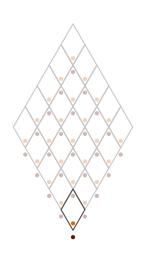

```mathematica
PlotLattice[lat1, UnitCells->5]
```

#### Build a graphene monolayer system (nearest neighbor)

```mathematica
sys1=BuildSystem[lat1, HoppingRange->1.01/√3, Onsite->(0&), Hopping->(-3.16 &)]
```

MQSystem[<NumberOfSites=2, SiteDimensions=1, LatticeDimensions=2>]

#### Plot bandstructure cut

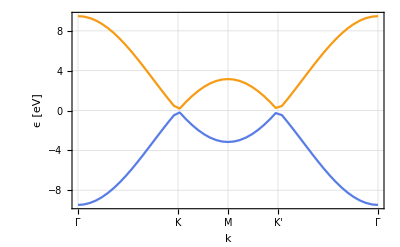

```mathematica
bands=Bands[sys1[2π z,-2π z],{z,0,1}];

PlotBands[bands,
 FrameLabel->{"k","ϵ [eV]"},
FrameTicks->{{Automatic,None},{{{0,"Γ"},{1/3,"K"},{1/2,"M"},{2/3,"K'"},{1,"Γ"}},None}}]
```

#### Plot bandstructure cut - naturally connected using eigenstates

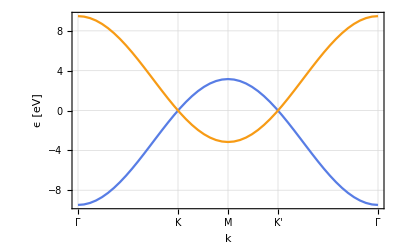

```mathematica
bands=UntangledBands[sys1[2π z,-2π z],{z,0,1}];

PlotBands[bands,
 FrameLabel->{"k","ϵ [eV]"},
FrameTicks->{{Automatic,None},{{{0,"Γ"},{1/3,"K"},{1/2,"M"},{2/3,"K'"},{1,"Γ"}},None}}]
```

#### Density of states

```mathematica
eigenvalues=Flatten[Table[Spectrum[sys1[2π z1, 2π z2]],{z1,0,1,.005},{z2,0,1,.005}]];
```

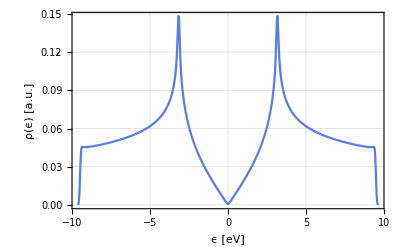

```mathematica
SmoothHistogram[eigenvalues,.05,
FrameLabel->{"ϵ [eV]","ρ(ϵ) [a.u.]"},
PlotDefaults]
```

## Demo 2: Graphene deformation superlattice

#### Build a honeycomb lattice with periodic deformation

```mathematica
L=32;
lat2=BuildLattice["Honeycomb", Supercell->{{L,0},{0,L}}, EmbeddingDimensions->3]
```

MQLattice[<NumberOfSites=2048, LatticeDimensions=2, EmbeddingDimensions=3>]

```mathematica
PlotLattice[lat2,ViewPoint->{2,0,.7}, ImageSize->400]
```

-Graphics3D-

```mathematica
displacement[{x_,y_, z_}]=With[{h=6,σ=5},{0,0,1}h ⅇ^(-1/2 Norm[{x,y,z}-L{0,√3/2,0}]^2/σ^2)];
lat2b=TransformLattice[lat2,#+displacement[#]&]
```

MQLattice[<NumberOfSites=2048, LatticeDimensions=2, EmbeddingDimensions=3>]

```mathematica
PlotLattice[lat2b,LinkRadius->.1, SiteRadius->.3, ViewPoint->{2,0,.7},ImageSize->400]
```

-Graphics3D-

#### Build system

```mathematica
sys2[β_]=BuildSystem[lat2b,
 HoppingRange->1.4/√3,
Hopping->(-3.16 ⅇ^(-β(Norm[#1-#2]/(1/√3)-1))&), 
Onsite->(0&)]
```

MQSystem[<NumberOfSites=2048, SiteDimensions=1, LatticeDimensions=2>]

#### Visualizing hoppings

```mathematica
PlotLattice[lat2b,sys2[0],
UnitCells->1,
LinkRadius->.2,
SiteRadius->0,
ImageSize->400,
Boxed->False,
ViewPoint->{2,0,.7}]
```

-Graphics3D-

#### Plot bandstructure cut

```mathematica
bandsβ0=UntangledBands[sys2[0][2π z,-2π z],{z,0,1}, Levels->20];
bandsβ3=UntangledBands[sys2[3.][2π z,-2π z],{z,0,1}, Levels->20];
```

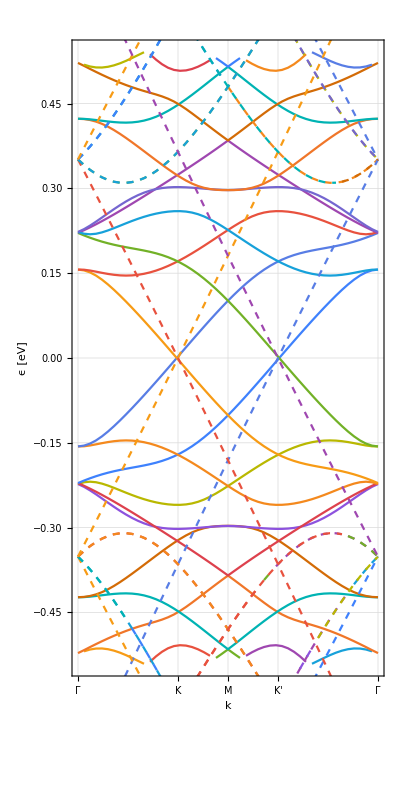

```mathematica
PlotBands[bandsβ0,PlotStyle->Dashed];
PlotBands[bandsβ3,
AspectRatio->2,
FrameLabel->{"k","ϵ [eV]"},
FrameTicks->{{Automatic,None},{{{0,"Γ"},{1/3,"K"},{1/2,"M"},{2/3,"K'"},{1,"Γ"}},None}}];
Show[%,%%]
```

## Demo 3: Berry curvature in Haldane’s model

#### Build a honeycomb lattice

```mathematica
lat3=BuildLattice["Honeycomb"]
```

MQLattice[<NumberOfSites=2, LatticeDimensions=2, EmbeddingDimensions=2>]

#### Build Haldane system

```mathematica
Haldane[r_, tag_]:=With[{λ=0.3, t=3.16},If[Norm[r]≤1/√3,t,ⅈ λ Cos[3ArcTan@@r]If[tag==="A",1,-1]]]
sys3=BuildSystem[lat3, HoppingRange->1.01,Onsite->(0&),Hopping->(Haldane[#1-#2,#3]&)]
```

MQSystem[<NumberOfSites=2, SiteDimensions=1, LatticeDimensions=2>]

#### Bandstructure in 2D

```mathematica
bands=Bands[sys3[{kx,ky}.{Cos[π/3],Sin[π/3]},{kx,ky}.{-Cos[π/3],Sin[π/3]}],{kx,-(4π)/3,(4π)/3},{ky,-(4π)/3,(4π)/3}, SamplePoints->50];

ListPlot3D[bands,
AxesLabel->{"k_x","k_y","ϵ[eV]"},
BoxRatios->{1,1,1},
PlotDefaults]
```

-Graphics3D-

#### Berry curvature (discrete algorithm) T. Fukui and Y. Hatsugai and H. Suzuki - J. Phys. Soc. Jpn. 74 1674-1677 (2005)

```mathematica
berrymesh=BerryMesh[sys3,SamplePoints->50];
```

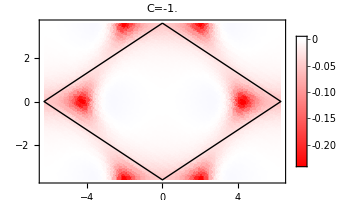
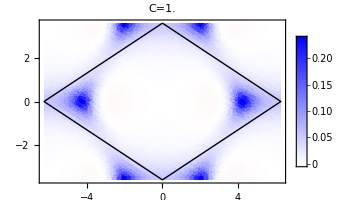

```mathematica
Column@PlotBerryMesh[lat3, berrymesh, PlotLegends->Automatic, ImageSize->300]
```

## Demo 4: Kane-Mele graphene nanoribbon (chiral edges)

#### Build a chiral honeycomb nanoribbon

MQLattice[<NumberOfSites=434, LatticeDimensions=1, EmbeddingDimensions=2>]

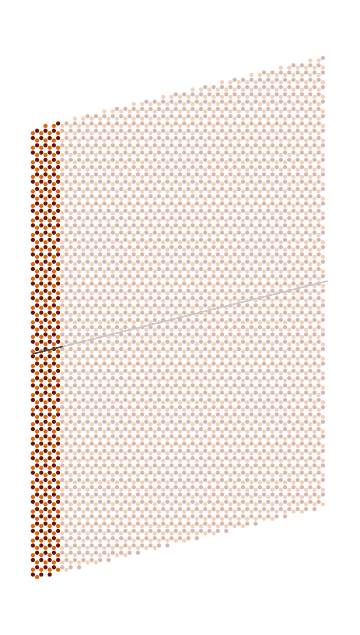

```mathematica
W=52; ChiralIntegers={4,-3}; RibbonAxis=Normalize[({{Cos[π/3], Cos[2π/3]}, {Sin[π/3], Sin[2π/3]}}).ChiralIntegers];

lat4=BuildLattice["Honeycomb", Supercell->{ChiralIntegers,{1,1}},Bounded->{Axes->{2},Region->(-W/2<=#.({{0, -1}, {1, 0}}).RibbonAxis<=W/2&)}]

PlotLattice[lat4, UnitCells->10, ImageSize->Medium, PlotDirectives->PointSize[Medium]]
```

#### Build Kane-Mele system

```mathematica
KaneMele[r_, tag_]:=With[{λ=0.1, t=3.16},If[Norm[r]≤1/√3,t({{1, 0}, {0, 1}}),ⅈ λ ({{1, 0}, {0, -1}})Cos[3ArcTan@@r]If[tag==="A",1,-1]]]
sys4=BuildSystem[lat4, HoppingRange->1.01,Onsite->(({{0, 0}, {0, 0}})&),Hopping->(KaneMele[#1-#2,#3]&)]
```

MQSystem[<NumberOfSites=434, SiteDimensions=2, LatticeDimensions=1>]

#### Plot bands

```mathematica
bands4=UntangledBands[sys4[2π z],{z,0,1}, Levels->60];
```

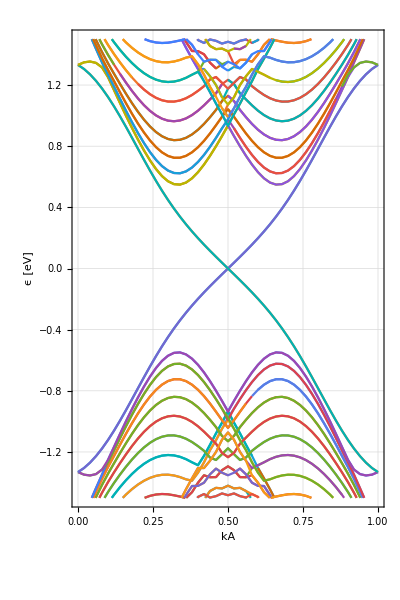

```mathematica
PlotBands[bands4, FrameLabel->{"kA","ϵ [eV]"}, PlotRange->{-1.5,1.5}, AspectRatio->1.5]
```

#### Edge modes

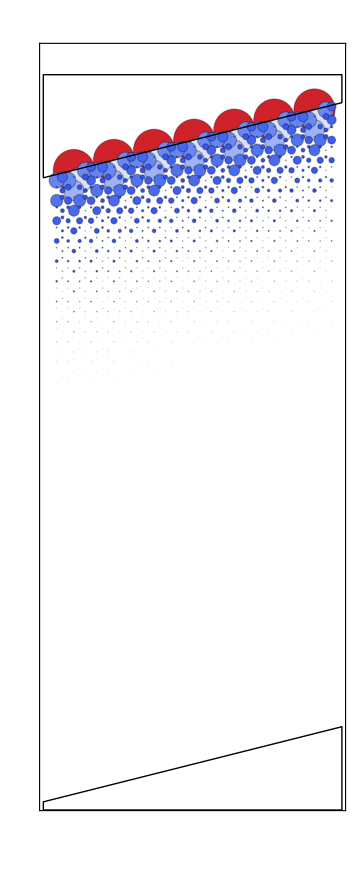
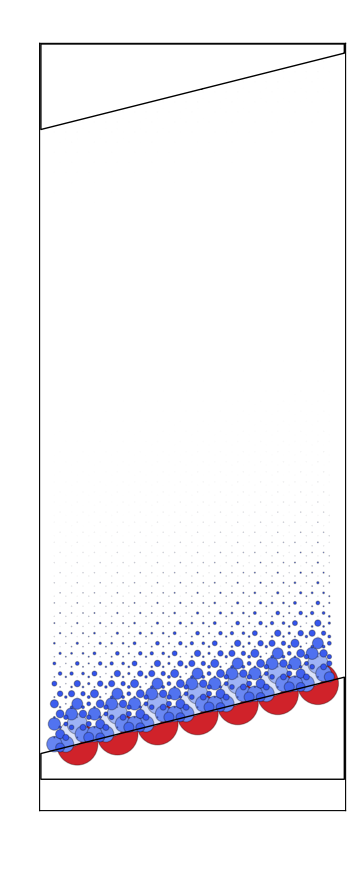

```mathematica
With[{z=0.51},PlotEigenstates[lat4,sys4[2π z],
Levels->2,
BubblePlot->True,
UnitCells->7,
ImageSize->Medium,
MaskRegion->(-W/2<=#.({{0, -1}, {1, 0}}).RibbonAxis<=W/2&),MaskStyle->None]]
```

## Demo 5: Magnetotransport through chaotic cavity

#### Build three lattices: left lead, central region, right lead

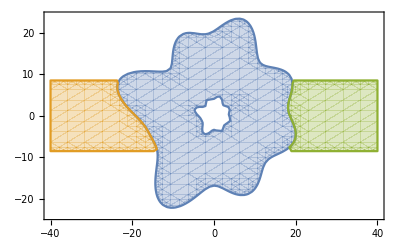

```mathematica
W=17;L=20;

SeedRandom[0];
central[θ_?NumericQ]=With[{n=10},L(1+1/n Total[RandomReal[{-1,1},n]Cos[Range[0,n-1] θ-π RandomReal[{-1,1},n]]])];
central[{x_,y_}]=1/5 central[ArcTan@@{x,y}]<=Norm[{x,y}]≤central[ArcTan@@{x,y}];
leadL[{x_,y_}]:=x<-L/2 && !central[{x,y}]&&(-W/2≤y≤W/2)
leadR[{x_,y_}]:=x>L/2 && !central[{x,y}]&&(-W/2≤y≤W/2)

RegionPlot[{central[{x,y}],leadL[{x,y}],leadR[{x,y}]},{x,-2 L,2 L},{y,-1.2 L,1.2 L}, AspectRatio->Automatic]
```

```mathematica
latL=BuildLattice["Honeycomb",Supercell->{{-1,1},{1,1}},
Bounded->{Axes->{2},Region->(-W/2≤#[[2]]≤W/2&)},
Reshape->{Axis->1,Region->(leadL[#]&), Seed->{-1.02 central[π],0}}]

latR=BuildLattice["Honeycomb",Supercell->{{1,-1},{1,1}},
Bounded->{Axes->{2},Region->(-W/2≤#[[2]]≤W/2&)},
Reshape->{Axis->1,Region->(leadR[#]&), Seed->{1.02 central[0],0}}]

latC=BuildLattice["Honeycomb",Bounded->{Axes->All,Region->(central[#]&),Seed->{.6 central[0],0}}]
```

MQLattice[<NumberOfSites=40, LatticeDimensions=1, EmbeddingDimensions=2>]

MQLattice[<NumberOfSites=40, LatticeDimensions=1, EmbeddingDimensions=2>]

MQLattice[<NumberOfSites=2747, LatticeDimensions=0, EmbeddingDimensions=2>]

#### Visualize lattice

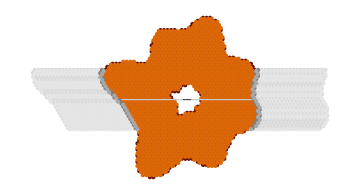

```mathematica
PlotLattice[{latC,latL,latR}, UnitCells->20, ImageSize->Medium, PlotDirectives->PointSize[Small]]
```

#### Build system with a magnetic field

```mathematica
PeierlsLandau[B_,r1_,r2_]:=ⅇ^(ⅈ B{-((r1+r2)/2)[[2]],0}.(r1-r2))
scatsys[B_]=BuildScatteringSystem[latC,{latL,latR},HoppingRange->1.01/√3,Onsite->(0&), Hopping->(PeierlsLandau[B,#1,#2]&)]
```

MQScatteringSystem[<NumberOfLeads=2, CentralSites=2747, LeadSites={40, 40}, Nambu=False>]

#### Interactive bandstructure of the leads, as a function of magnetic field

```mathematica
Manipulate[
PlotBands[UntangledBands[scatsys[B]["Leads"]⟦1⟧[2π z],{z,0,1},Levels->All], 
PlotRange->{-1,1},
FrameLabel->{"kA/2π","ϵ/t"},
GridLines->{None,{.1}},
ImageSize->Medium],
{B,0,0.2}]
```

#### Compute transport

```mathematica
G0=Sample[Conductance[ω,scatsys[0]],{ω,0.01,2}, SamplePoints->60];
G1=Sample[Conductance[ω,scatsys[.2]],{ω,0.01,2}, SamplePoints->60];
```

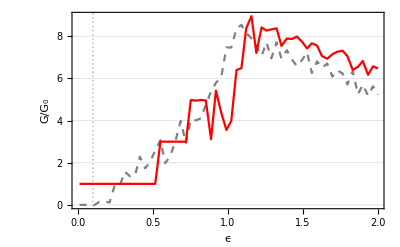

```mathematica
ListLinePlot[{G0,G1}, 
PlotStyle->{{Dashed,Gray},Red},
GridLines->{{.1},Automatic},
FrameLabel->{"ϵ","G/G_0"},
PlotDefaults]
```

#### Visualize scattering states

```mathematica
states0=ScatteringStates[.1,scatsys[0], LeadCells->25]
states1=ScatteringStates[.1,scatsys[.2], LeadCells->25]
```

MQScatteringStates[<PropModes={1, 1}, NumberOfLeads=2, LeadCells={{25, 25}, {25, 25}}>]

MQScatteringStates[<PropModes={1, 1}, NumberOfLeads=2, LeadCells={{25, 25}, {25, 25}}>]

Without magnetic flux

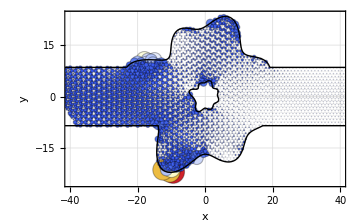

```mathematica
PlotScatteringStates[{latC,latL,latR},states0, 
ImageSize->Medium,
BubblePlot->True,
MaskRegion->((central[#]||leadL[#]||leadR[#])&),
MaskStyle->None,
PlotRange->{{-2L,2L},Automatic}]
```

With magnetic flux

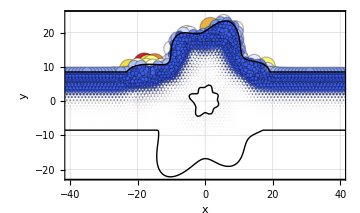

```mathematica
PlotScatteringStates[{latC,latL,latR},states1, 
ImageSize->Medium,
BubblePlot->True,
MaskRegion->((central[#]||leadL[#]||leadR[#])&),
MaskStyle->None,
PlotRange->{{-2L,2L},Automatic}]
```

... and with a different visualization style

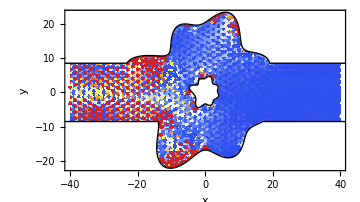

```mathematica
PlotScatteringStates[{latC,latL,latR},states0, 
ImageSize->Medium,
BubblePlot->False,
PlotLegends->False, 
InterpolationOrder->0, 
MaskRegion->((central[#]||leadL[#]||leadR[#])&),
PlotRange->{{-2L,2L},Automatic}]
```

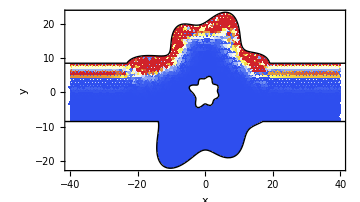

```mathematica
PlotScatteringStates[{latC,latL,latR},states1, 
ImageSize->Medium,
BubblePlot->False,
PlotLegends->False, 
InterpolationOrder->0, 
MaskRegion->((central[#]||leadL[#]||leadR[#])&),
PlotRange->{{-2L,2L},All}]
```